```mathematica
(*Harmonic-Oscillator*)
```

```mathematica
(*m=1,ω=1*)
V[r_]=1/2 r^2;α=2;
```

```mathematica
(*The analytic result is Subscript[E, n]=n+1/2*)
```

```mathematica
EHO=Module[{d=100,n=20,ev1,ev2,ev},ev1=NDEigenvalues[{V[r] f[r]-1/α f''[r],DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01(*This is how NDEigenvalues controls the accuracy.*)}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];(*Odd*)
ev2=NDEigenvalues[{V[r] f[r]-1/α f''[r]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01(*This is how NDEigenvalues controls the accuracy.*)}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];(*Even*)
ev=Riffle[ev2,ev1]
]
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5,15.5,16.5,17.5,18.5,19.5,20.5,21.5,22.5,23.5,24.5,25.5,26.5,27.5,28.5,29.5,30.5,31.5,32.5,33.5,34.5,35.5,36.5,37.5,38.5,39.5}

```mathematica
(*error*)
```

```mathematica
Table[n+0.5,{n,0,39}]-EHO
```

{-1.16293×10^-11,-9.02241×10^-11,-3.23889×10^-10,-8.19143×10^-10,-1.67809×10^-9,-3.00628×10^-9,-4.90617×10^-9,-7.48337×10^-9,-1.08413×10^-8,-1.50838×10^-8,-2.03153×10^-8,-2.66402×10^-8,-3.41622×10^-8,-4.29853×10^-8,-5.32137×10^-8,-6.49516×10^-8,-7.83033×10^-8,-9.33721×10^-8,-1.10263×10^-7,-1.29079×10^-7,-1.49925×10^-7,-1.72905×10^-7,-1.98122×10^-7,-2.25682×10^-7,-2.55687×10^-7,-2.88242×10^-7,-3.23451×10^-7,-3.61418×10^-7,-4.02247×10^-7,-4.46042×10^-7,-4.92907×10^-7,-5.42946×10^-7,-5.96263×10^-7,-6.52962×10^-7,-7.13148×10^-7,-7.76923×10^-7,-8.44392×10^-7,-9.1566×10^-7,-9.90829×10^-7,-1.07×10^-6}

```mathematica
(*Coulomb Potential*)
```

```mathematica
V[r_]=-14.3996448504451555789912633575295935414`6.88249108029756/r;α=0.26246843532124502683678435500618410715`6.076375074285658;
```

```mathematica
(*The analytic result is Subscript[E, n]=Subscript[E, 1]/n^2*)
(*The first few energy*)
Ehydrogen=Table[(-QuantityMagnitude[UnitConvert[Quantity[1,"Rydbergs"],"eV"]])/n^2,{n,40}]
```

{-13.6057,-3.40142,-1.51174,-0.850356,-0.544228,-0.377936,-0.277667,-0.212589,-0.167972,-0.136057,-0.112444,-0.094484,-0.0805071,-0.0694168,-0.0604697,-0.0531472,-0.0470785,-0.0419929,-0.0376889,-0.0340142}

```mathematica
(*code*)
```

```mathematica
EhNDE=Module[{shift=10,d=1000,n=20,ev,evshifted},(*The shift is to move the eigenvalues away from 0 so that the program can sort the eigenvalues in a right way.*)ev=NDEigenvalues[{shift f[r]+V[r] f[r]-1/α f''[r],DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01(*This is how NDEigenvalues controls the accuracy.*)}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evshifted=ev-shift]
```

{0.000246547,-0.0019213,0.0025156,-0.00398506,0.00488349,-0.00594117,0.00734822,-0.00778511,-0.0095109,0.00990809,-0.0111104,0.0125616,-0.0125722,-0.013884,-0.0150554,0.0153076,-0.0161716,-0.0173539,0.0181448,-0.0186635}

```mathematica
(*error*)
```

```mathematica
Ehydrogen-EhNDE
```

{-4.08613×10^-9,3.62577×10^-9,2.09019×10^-9,1.31383×10^-9,8.84023×10^-10,6.35278×10^-10,4.84689×10^-10,3.82127×10^-10,3.12891×10^-10,2.61963×10^-10,2.22333×10^-10,1.93403×10^-10,1.70382×10^-10,1.52821×10^-10,1.37016×10^-10,1.24191×10^-10,1.13582×10^-10,1.03948×10^-10,9.435×10^-11,8.67227×10^-11}

```mathematica
(*My fitted potential*)
```

```mathematica
V[r_]=-(1/r)-(1.0415223038416566 E^(-0.9990999998788636 r))/r;α=2.;
```

```mathematica
(*This is code*)
Module[{shift=10,d=1500,n=20,ev,evShifted},ev=NDEigenvalues[{shift f[r]+V[r] f[r]-1/α f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.01}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift]
```

```mathematica
(*These are results with different d.The last one has a different MaxCellMeasure of 0.001,proves that the accuracy of lower energy mainly relys on b.*)
```

```mathematica
(*d=1500*)
{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.0012937}

(*d=1000*)
{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.0026799,-0.00232673,-0.00203904,-0.00180159,-0.00160333,-0.00143608,-0.00129369}

(*d=500&MaxCellMeasure->0.001*)
{-1.33732,-0.186434,-0.0710575,-0.0374072,-0.023051,-0.0156184,-0.0112778,-0.00852433,-0.00666881,-0.00535929,-0.0044008,-0.00367822,-0.00312003,-0.00267982,-0.0023228,-0.00199518,-0.00162513,-0.0011884,-0.000689036,-0.000132268}
```

```mathematica
(*Eigenvectors for Coulomb Potential(WIP!)*)
```

```mathematica
V[r_]=-14.3996448504451555789912633575295935414`6.88249108029756/r;α=0.26246843532124502683678435500618410715`6.076375074285658;
a=0.52917721036724619261935939416491622623`6.45296897443304;
```

```mathematica
AbsoluteTiming[Module[{shift=20,d=2000,n=6,ev},(*The shift is to move the eigenvalues away from 0 so that the program can sort the eigenvalues in a right way.*){ev,ef}=NDEigensystem[{shift f[r]+V[r] f[r]-1/α f''[r],DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.001(*This is how NDEigenvalues controls the accuracy.*)}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evshifted=ev-shift]]
```

Flatten::normal: Flatten[NDSolve`FEM`ElementMeshDump`regionHoles,1] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[NDSolve`FEM`ElementMeshDump`regionHoles,1.] 中的位置 1 处应该是非原子表达式.

Flatten::normal: Flatten[Automatic,1.] 中的位置 1 处应该是非原子表达式.

General::stop: 在本次计算中，Flatten::normal 的进一步输出将被抑制.

{852.992,{-13.6057,-3.40142,-1.51174,-0.850356,-0.544228,-0.377936}}

```mathematica
(*Check for normalization*)
```

```mathematica
Table[NIntegrate[ef[[n]]^2,{r,0,1000}],{n,20}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
(*Analytic Hydrogen atom wavefunction*)
```

```mathematica
R[n_,r_]=FullSimplify[2/(a^(3/2) n^2 (2 l+1)!) Sqrt[(n+l)!/(n-l-1)!] E^(-1/2 (2 r)/(n a)) ((2 r)/(n a))^l Hypergeometric1F1[-n+l+1,2 l+2,(2 r)/(n a)]];
u[n_,r_]=r R[n,r]/.l->0
```

(5.19551 ⅇ^(-(1.88973 r)/n) r √(Gamma[1+n]/Gamma[n]) Hypergeometric1F1[1-n,2,(3.77945 r)/n])/n^2

```mathematica
(*Comparasion*)
```

```mathematica
Table[u[n,r]-ef[[n]]/.r->0.5,{n,20}]
```

{-0.00179939,0.0805576,0.0552369,0.0383865,0.116992,0.0881797,0.0178567,0.0566664,0.0473308,0.0107518,0.0348645,0.00826648,0.00736111,0.0241771,0.0217778,0.0197508,0.00497911,0.00457942,0.00423047,0.0140956}

```mathematica
(*Obviously this result isn't good.It needs more work.*)
```

```mathematica
NIntegrate[ef[[1]]D[ef[[1]],{r,4}],{r,0,∞}]
```

NIntegrate::izero: 在所有积分子区域上，积分和误差估计都是 0. 请尝试增加 MinRecursion 选项的值. 如果积分值可能是 0，为 AccuracyGoal 选项指定一个有限制.

0.

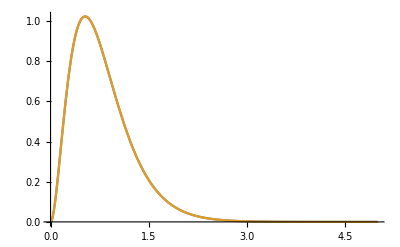
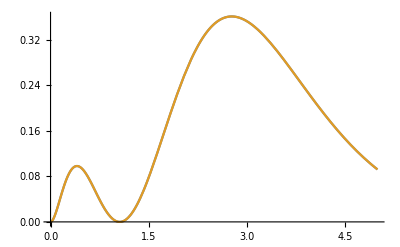
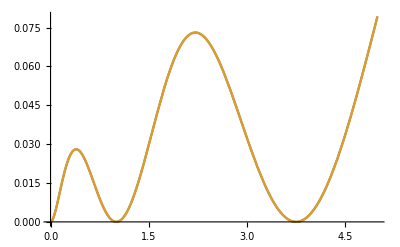
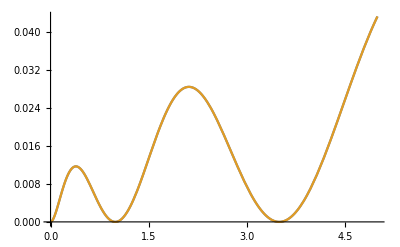
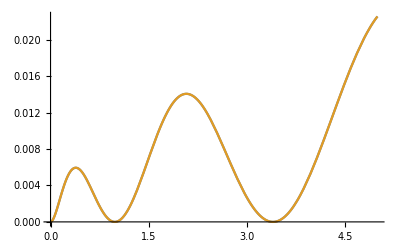
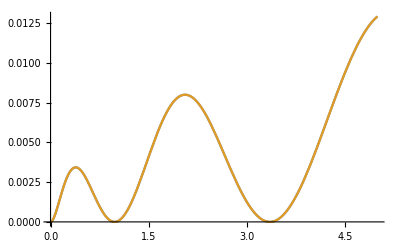

```mathematica
Table[Plot[{ef[[n]]^2,u[n,r]^2},{r,0,5}],{n,6}]
```